# Lista I - Mecânica Estatística

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

## 1.

Nesse exercício temos inicialmente que o nosso espaço amostral é composto por Ω^1= {10 pc quebrados, 90 pc funcionando} , ou seja, nosso espaço amostral tem 100 elementos. A probabilidade de eu tirar um elemento d meu espaço amostral e ele ser um PC funcionando é de:
Pr_1[Ω^1]= (Numero de pc que funcionam)/(Numero de pc) = 90/100 = 0,9
Agora, para calcular a probabilidade do segundo PC estar funcionando, deve levar em consideração que o meu espaço amostral não é mais o mesmo,   Ω^2= {10 pc quebrados, 89 pc funcionando}, com isso a probabilidade de um segundo PC tirado desse espaço amostral estar funcionando é de:
Pr_2[Ω^2]= (Numero de pc que funcionam)/(Numero de pc) = 89/99 
Com isso, podemos ir calculando a probabilidade individual de cada PC tirado da sequência estar funcionado
Pr_3 = 88/98 ; 	Pr_4 = 87/97 ;		Pr_5 = 86/96 ;		Pr_6 = 85/95 ;		Pr_7 = 84/94 ;		Pr_8 = 83/93 ;		Pr_9 = 82/92 ;		Pr_10 = 81/91 ;
Visto isso, temos que, nossa probabilidade é do tipo dependente, ela depende de que todos os Pr_x. Assim, a probabilidade do nosso exercício é:
Pr = 90/100*88/98* 87/97*86/96* 85/95* 84/94* 83/93*82/92*81/91  = (90!)/(80!)*(90!)/(100!) = 0,330476
Ou seja, a nossa probabilidade vai ser de aproximadamente 33%

```mathematica
N[((90!)^2)/(100! * 80!)]
```

0.330476

## 2.

Nesse exercício nos termos dois espaços amostrais:  Ω^(Urna 1) = {5 bolas brancas, 7 bolas pretas} , que possui 12 elementos, e Ω^Urna2 = {3 bolas brancas, 12 bolas pretas}, que possui 17 elementos. A Urna 1 é escolhida quando a moeda dá cara e a Urna 2 é escolhida quando a moeda dá coroa. No entanto, nossa moeda não é honesta, ela possui uma probabilidade de  4/10 de sair cara.
O exercício 2suponha que uma bola branca foi escolhida, perguntando qual a probabilidade de que no lançamento da moeda o resultado tenha sido coroa ? Para isso devemos lembrar do teorema de Bayes que é usado para saber a probabilidade de um evento A acontecer, sabendo que B já aconteceu. No nosso caso, temos:
	●	B será a bola branca escolhida.
	●	A será a moeda dar coroa.
Pr[A|B]=(Pr[B|A]*Pr[A])/(Pr[B|A]*Pr[A]  +  Pr[B|Ā]*Pr[Ā])
Calcularemos agora cada termo do teorema de Bayes:
— Pr[B]=Probabilidade da bola ser branca=(Numero de bolas brancas)/(Numero de bolas)= 3/27
— Pr[A]=Probabilidade da moeda ser coroa=6/10
— Pr[ A^- ]=1 - Pr[A]=Probabilidade da moeda ser cara=4/10
— Pr[B|A]=Probabilidade da bola branca  sair da urna 2 =(Numero de bolas brancas)/(Numero de bolas na urna 2)= 3/15
— Pr[B|A^- ]=Probabilidade da bola branca  sair da urna 1 =(Numero de bolas brancas)/(Numero de bolas na urna 1)= 5/12
Assim, temos que a probabilidade de que a moeda tenha sido coroa é de aproximadamente 42%.
Pr[A|B]=(Pr[B|A]*Pr[A])/(Pr[B|A]*Pr[A]  +  Pr[B|Ā]*Pr[Ā]) = ((3/15)*(6/10))/((3/15)*(6/10) +  (5/12)*(4/10)) = (3/25)/((3/25) + (1/6))= 0,4186

```mathematica
N[ (3/25)/((3/25) + (1/6))]
```

0.418605

## 3.a)

Nosso dado possui 6 fases e não é honesto, sendo que a probabilidade de sair o valor 6 é p e a probabilidade de sair o numero 1,2,3,4 e 5 é q para cada um desses valores. Assim, temos que o meu espaço amostral é Ω= {x_1 = 1,x_2 = 2,x_3 = 3,x_4 = 4,x_5 = 5,x_6 = 6}, onde a nossa variável aleatória é x ∈ Ω.
Pr[Ω] =∑_(x ∈ Ω) Pr[x] = ∑_(i=1)^6 Pr[x] = 5q +p = 1
Dessa normalização temos que: q = (1-p)/5

## 3.b)

A distribuição de probabilidade de x, em termos de Delta de Dirac para o nosso espaço amostral Ω, dado:
δ(x - x_i) = Piecewise[{{0, , x ≠ x_i}, {∞, , x = x_i}}]  		e		p_i = Piecewise[{{q = (1-p)/5, para i=1,2,3,4,5}, {p, para i=6}}]
P_Ω[x] = ∑_(i=1)^6 p_i δ(x - x_i)

## 3.c)

Sabendo que, ∫_(-∞)^∞ f(x) δ(x - x_i) ⅆx  = f(x_i) e ∫_(-∞)^∞ δ(x - x_i) ⅆx  = 1
Calculando o valor médio de x:
x^- = ⟨x⟩ = ∫_(-∞)^∞ xP_Ω[x] ⅆx= ∫_(-∞)^∞ ∑_(i=1)^6 x p_i δ(x - x_i) ⅆx= ∑_(i=1)^6 p_i∫_(-∞)^∞ x δ(x - x_i) ⅆx = ∑_(i=1)^6 p_i x_i= x_1 p_1+ x_2 p_2+ x_3 p_3+ x_4 p_4+ x_5 p_5+ x_6 p_6= 15q +6p=15*(1-p)/5 +6p = 3 +3p
Calculando o desvio padrão:
(Δx)^2 = ∫_(-∞)^∞ (x- x^-)^2 P_Ω[x] ⅆx =  ∫_(-∞)^∞ (x^2 + (x^-)^2-2 x x^-)P_Ω[x] ⅆx =  ∫_(-∞)^∞ (x^2 + (x^-)^2-2 x x^-)∑_(i=1)^6 p_i δ(x - x_i)   ⅆx =  ∑_(i=1)^6 p_i[∫_(-∞)^∞ x^2 δ(x - x_i)   ⅆx  + ∫_(-∞)^∞ (x^-)^2 δ(x - x_i)   ⅆx + ∫_(-∞)^∞ ( -2 x x^-)δ(x - x_i)   ⅆx ]=∑_(i=1)^6 p_i[x_i^2+ (x^-)^2 -2 x_i x^- ]  =q(1 + (3 +3p)^2 - 2 (3+3p)) + q(4+ (3 +3p)^2 - 4 (3+3p)) + q(9 + (3 +3p)^2 - 6 (3+3p)) + q(16 + (3 +3p)^2 - 8 (3+3p)) + q(25 + (3 +3p)^2 - 10 (3+3p)) +  p(36 + (3 +3p)^2 - 12 (3+3p))  = 
[(1-p)/5](5[9 +9 p^2 +18p] + 55-90 -90p) + p(36+9+9 p^2 +18p -36-36p) = -9 p^2+7p +2
Δx = √(-9 p^2+7p +2)

## 3.d)

Testando para o caso particular, onde o nosso dado é honesto, ou seja, a probabilidade será p = 1/6. O nosso valor médio e desvio padrão, será então:
x^- = 3 + 3p = 3 +3/6 = 7/2 =3,5 		e		 Δx = √(-9 p^2+7p +2) = √(-9/36+7/6+2)  =  √(2,92) = 1,7

```mathematica
N[ √(-9/36+7/6+2)]
```

1.70783

## 4.

Temos nossa variável aleatória x,onde x ∈ (0,1). Sabemos que a formula da distribuição de probabilidade uniforme no intervalo (a,b) é dado por: Pr_generalizada = 1/(b-a)Piecewise[{{0, se x< a e x>b}, {1, se a≤x≤b}}].  Assim, a distribuição de probabilidade para a nossa variável x é dada por:
Pr_X[x] = 1Piecewise[{{0, se x< 0 e x>1}, {1, se 0≤x≤1}}]
Para a distribuição de probabilidade da variável y=Y(x)=ln(x) ⟶ χ = Y^-1(y)=e^y. O nosso intervalo para y será: y = ln(x) ⟶ y ∈ (ln(0), ln(1))=(-∞,0). Para descobrir a distribuição de probabilidade de y = ln(x), vou utilizar a seguinte expressão:
Py_Y(y) = Pr_X(χ) (|dy/dx|)_(y = Y(x))^-1= Pr_X(e^y) (|(d(ln(x)))/dx|)_(y = Y(x))^-1 =Pr_X(e^y) (|1/x|)_(y = Y(x))^-1 =Pr_X(e^y) (|1/e^y|)^-1=Pr_X(e^y) e^y 
Disso, eu tiro que a minha probabilidade de y é: Pr_X[x] = e^y Piecewise[{{0, se x>0}, {1, se x≤0}}]

## 5.a)

Maior parte das reações ocorrem próximas ao centro. PAra uma região de raio menor que R = 5*10^8 m  o processo pode ser considerado uma caminhada aleatória. Sendo a velocidade do fóton igual a da luz, c = 299792,4 Km/s, e o passo do fóton l = 1mm = 10^-3 m = 10^-6 Km. Quero saber quantos passos ele leva para ir da origem para R, sabendo que a partícula percorrerá um caminho aleatório (a cada passo ele vai para um caminho diferente).
Considerando que a caminhada ocorre em coordenadas esféricas, o primeiro passo do fóton terá as seguintes coordenadas>
x_1 = l sin(ϕ_1)cos(θ_1) ; y_1 = l sin(ϕ_1)sin(θ_1) ; z_1 = l cos(ϕ_1); 0≤ϕ_1≤ π e 0≤θ_1≤ 2π, onde ϕ_1 e θ_1 são os ângulos que indicam a direção dos passos.
Depois de N passos dados, eu tenho que:
x_ = l ∑_(i=1)^N sin(ϕ_i)cos(θ_i) ; y = l ∑_(i=1)^N sin(ϕ_i)sin(θ_i) ; z = l ∑_(i=1)^N cos(ϕ_i); 
A distância média percorrida por esses passos é:
⟨r^2 ⟩=⟨ x^2+ y^2 + z^2⟩ = ⟨l^2[(∑_(i=1)^N sin(ϕ_i)cos(θ_i))^2 + (∑_(i=1)^N sin(ϕ_i)sin(θ_i))^2 + (∑_(i=1)^N cos(ϕ_i))^2]⟩
Abaixo colocarei a resolução do exponencial desse somatório individualmente, lembrando que como as direções de ϕ_1 e θ_1  são aleatoriamente distribuídas e independentes, podemos dizer que pela ortogonalidade das funções trigonométricas, temos que: ∑_(i≠j) sin(ϕ_i)sin(ϕ_j) = ∑_(i≠j) cos(θ_i)cos(θ_j) = 0
Disso, teremos que:

■	(∑_(i=1)^N sin(ϕ_i)cos(θ_i))^2 = (sin(ϕ_1)cos(θ_1) + sin(ϕ_2)cos(θ_2)+ ... + sin(ϕ_N)cos(θ_N))^2  = ∑_(i=1)^N sin^2(ϕ_i)cos^2(θ_i) + ∑_(i≠j) sin(ϕ_i)cos(θ_i)sin(ϕ_j)cos(θ_j) =  ∑_(i=1)^N sin^2(ϕ_i)cos^2(θ_i) + ∑_(i≠j) sin(ϕ_i)sin(ϕ_j)∑_(i≠j) cos(θ_i)cos(θ_j)=  ∑_(i=1)^N sin^2(ϕ_i)cos^2(θ_i) 

■	(∑_(i=1)^N sin(ϕ_i)sin(θ_i))^2 = (sin(ϕ_1)sin(θ_1) + sin(ϕ_2)sin(θ_2)+ ... + sin(ϕ_N)sin(θ_N))^2  = ∑_(i=1)^N sin^2(ϕ_i)sin^2(θ_i) + ∑_(i≠j) sin(ϕ_i)sin(θ_i)sin(ϕ_j)sin(θ_j) =  ∑_(i=1)^N sin^2(ϕ_i)sin^2(θ_i) + ∑_(i≠j) sin(ϕ_i)sin(ϕ_j)∑_(i≠j) sin(θ_i)sin(θ_j)=  ∑_(i=1)^N sin^2(ϕ_i)sin^2(θ_i) 

■	(∑_(i=1)^N cos(ϕ_i))^2 = (cos(ϕ_1)+ cos(ϕ_2)+ ... + cos(ϕ_N))^2  = ∑_(i=1)^N cos^2(ϕ_i) + ∑_(i≠j) cos(ϕ_i)cos(ϕ_j) =   ∑_(i=1)^N cos^2(ϕ_i)

Com isso temos que:
⟨r^2 ⟩= ⟨x^2+ y^2 + z^2⟩ = ⟨l^2 ∑_(i=1)^N [sin^2(ϕ_i)cos^2(θ_i) +sin^2(ϕ_i)sin^2(θ_i) +cos^2(ϕ_i)] ⟩= ⟨ l^2 ∑_(i=1)^N [sin^2(ϕ_i) +cos^2(ϕ_i)] ⟩=  ⟨l^2 ∑_(i=1)^N 1  ⟩⟶ ⟨r^2⟩ = l^2 N
Assim, para r = R:
 N = R^2/l^2 = 2,5*10^23 passos

```mathematica
N[(25*10^16)/10^-6]
```

2.5×10^23

## 5.b)

O fóton percorre uma distância que pode ser medida multiplicando o tamanho dos seus passos por quantos passos ele deu:
Distância = lN = 2,5*10^23*10^-6 = 2,5*10^17 Km
Para descobrir quando anos um fóton levaria em média para chegar até R, devemos usar a relação ΔS=v*t, onde a v é a velocidade do fóton. Assim, temos:
Tempo = Distância/c = (2,5*10^17 Km)/(299792,4 Km/s) =8,3391*10^11 s =  8,3391*10^11 *3,171*10^-8 anos = 26443,3  anos

```mathematica
N[ (2.5*10^17)/299792.4]
```

8.3391×10^11

```mathematica
N[  8.3391*10^11 *3.171*10^-8 ]
```

26443.3

## 6.a)

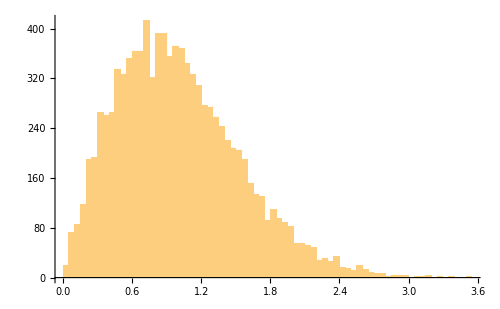

```mathematica
(*Definindo M, N, n, Subscript[λ, n+1] e Subscript[λ, n]*)
ClearAll[M,N0,n ,lis, r1]
M = 10001;
N0 = 2 ;(* Coloquei N0 para o matematica não confundir N com a função N*)
n = N0/2;
lis = {};
For[ i = 1, i<M, i++,mat=RandomVariate[NormalDistribution[],{N0,N0}]; matsim = (mat + Transpose[mat])/2;autovalores = Sort[Eigenvalues[matsim]];dif = autovalores[[n+1]] - autovalores[[n]];lis = Join[lis, {dif}];]
r1 = lis/Mean[lis];
his1 = Histogram[r1,50, ImageSize->500]
```

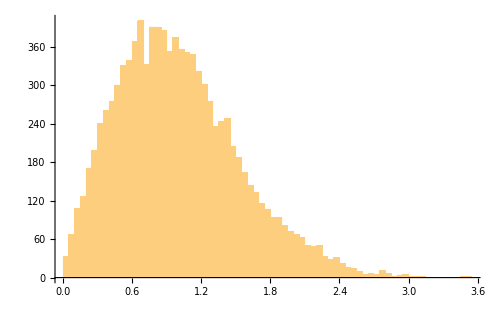

```mathematica
(*Definindo M, N, n, Subscript[λ, n+1] e Subscript[λ, n]*)
ClearAll[M,N0,n, lis, r2]
M = 10001;
N0 = 4 ;(* COloquei N0 para o matematica não confundir N com a função N*)
n = N0/2;
lis = {};
For[ i = 1, i<M, i++,mat=RandomVariate[NormalDistribution[],{N0,N0}]; matsim = (mat + Transpose[mat])/2;autovalores = Sort[Eigenvalues[matsim]];dif = autovalores[[n+1]] - autovalores[[n]];lis = Join[lis, {dif}];]
r2 = lis/Mean[lis];
his2 = Histogram[r2,50, ImageSize->500]
```

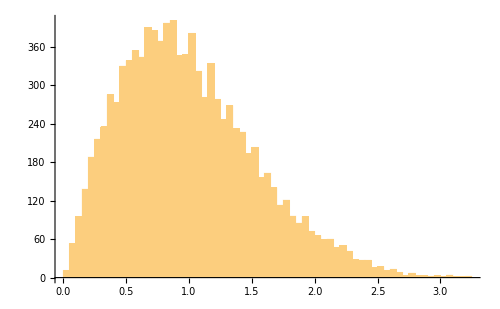

```mathematica
(*Definindo M, N, n, Subscript[λ, n+1] e Subscript[λ, n]*)
ClearAll[M,N0,n, lis, r3]
M = 10001;
N0 = 10 ;(* COloquei N0 para o matematica não confundir N com a função N*)
n = N0/2;
lis = {};
For[ i = 1, i<M, i++,mat=RandomVariate[NormalDistribution[],{N0,N0}]; matsim = (mat + Transpose[mat])/2;autovalores = Sort[Eigenvalues[matsim]];dif = autovalores[[n+1]] - autovalores[[n]];lis = Join[lis, {dif}];]
r3 = lis/Mean[lis];
his3 = Histogram[r3,50, ImageSize->500]
```

## 6.b)

Para encontrarmos os valores de H = (a | b
b | c), usamos a relação det(H -λI_n) = 0. Assim, teremos que:
det[a-λ
bb
c-λ] = 0 ⟶(a-λ)(c-λ) - b^2 = 0 ⟶ a c - a λ - c λ +λ^2  - b^2 = 0 ⟶   λ^2  - ( a + c )λ - b^2 + a c= 0 
Disso teremos que,  λ_± = ((a + c) ± √((a + c)^2 + 4(b^2 -a c)))/2. Assim, Δλ = λ_+ - λ_- =((a + c)  + √((a + c)^2 + 4(b^2 -a c)) - (a + c) + √((a + c)^2 + 4(b^2 -a c)))/2=√((a + c)^2 + 4(b^2 -a c))=√(a^2+2 a c + c^2 + 4 b^2 - 4 a c)= √(a^2-2 a c + c^2 + 4 b^2) = √((a - c)^2 + 4 b^2)

## 6.c)

Considerando que o valor de b, depende de dois números gaussianos, que possuem as seguintes distribuições de probabilidade independentes: P_a(u) = P_c(u) = 1/(√(2π))e^(-u^2/2). Assim, como foi dito no enunciado o número gaussiano b depende dos números gaussianos a e c, farei que eles possuem a seguinte relação: b = (a + c)/2. Disso, usarei a seguinte relação para obter a probabilidade de b:
P_b(u) = P_a(u)P_c(u) =  1/(2π)e^(-u^2) . Essa distribuição de probabilidade, ainda precisa ser normalizada, para isso farei:
 ∫_(-∞)^∞ cte *(e^(-u^2))/(2π)du =cte/(2π) ∫_(-∞)^∞ e^(-u^2)du =  cte/(2π) √π =1 ⟶ cte = (2π)/(√π)
Assim, nossa distribuição de probabilidade de b é: P_b(u) = 1/(√π)e^(-u^2)

```mathematica
∫_(-∞)^∞ ⅇ^(-u^2) ⅆu
```

√π

## 6.d)

Para P_a(a)=1/(√(2π))e^(-a^2/2);P_b(b)=1/(√(2π))e^(-b^2);P_c(c)=1/(√(2π))e^(-c^2/2). Temos que:
P_Δ(Δλ)= ∫_(-∞)^∞ da∫_(-∞)^∞ db∫_(-∞)^∞ dc δ(Δλ - √((c - a )^2 +4 b^2))P_a(a)P_b(b)P_c(c) = ∫_(-∞)^∞ da∫_(-∞)^∞ db∫_(-∞)^∞ dc δ(Δλ - √((c - a )^2 +4 b^2))(e^(-a^2/2 -b^2/2 -c^2/2))/(2 π^(3/2))
Realizando a mudança de variável: x = (c + a)/2 e y = (c-a)/2 ⟶ a=x-y e c= x+y. Terei que:
■	√((c - a )^2 +4 b^2) = √(4 y^2 + 4 b^2) = 2 √(y^2 + b^2)
■	a^2 +b^2+c^2 = 2 x^2 + 2 y^2+ b^2
Para fazer a mudança de variável da integral dupla, eu faço que d a d c = |(∂(a,c))/(∂(x,y))|d x d y, onde |(∂(a,c))/(∂(x,y))|é o módulo do Jacobiano, sendo ele: |(∂(a,c))/(∂(x,y))| = |(∂a)/(∂x)
(∂c)/(∂x)(∂a)/(∂y)
(∂c)/(∂y)| = |1
1-1
1|=2. Com isso, eu tenho que:  d a d c = |(∂(a,c))/(∂(x,y))|d x d y = 2 d x d y. Assim, nossa integral fica:
P_Δ(Δλ)= ∫_(-∞)^∞ dy∫_(-∞)^∞ dbδ(Δλ - 2 √(y^2 + b^2))∫_(-∞)^∞ dx (e^(-1/2(2 x^2 + 2 y^2+ b^2)))/π^(3/2) =∫_(-∞)^∞ dy∫_(-∞)^∞ dbδ(Δλ - 2 √(y^2 + b^2)) (e^(-1/2( 2 y^2+ b^2)))/π^(1/2)

```mathematica
∫_(-∞)^∞ Exp[(-2*x^2 - 2*y^2 - b^2)/2]ⅆx
```

ⅇ^(-b^2/2-y^2) √π